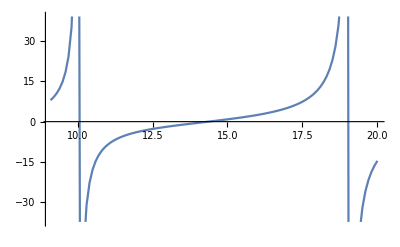

InterpolatingFunction[{{9.1, 20.}}, <>]

```mathematica
E1 = 4;
E2 = 2;
R =50;
P = 50;
Q = 50;
A = Table[0, {P}, {Q}, {R}];
B = Table[0, {P}, {Q}, {R}];
A[[1, 1, 1]] = 1;
B[[1, 1, 1]] = 1;
For [k = 1, k <= P, k++,
 For [j = 1, j <= Q, j++,
  For[i = 1, i <= R, i++,
   	 p = k - 1;
   	 q = j - 1;
   r = i - 1;
   Which[k == 1 &&  j == 1 && i > 1,
    					A[[1, 1, i]] = (1/(((E2 + 2)*r)*((E2 + 2)*r - 1)))*(-1)*A[[1, 1, i - 1]];
    					B[[1, 1, i]] = (1/(((E2 + 2)*r)*((E2 + 2)*r + 1)))*(-1)*B[[1, 1, i - 1]],
    	   k == 1 && j > 1 && i == 1,
    					A[[1, j, 1]] = (1/((2*q)*(2*q - 1)))*A[[1, j - 1, 1]];
    					B[[1, j, 1]] = (1/((2*q)*(2*q + 1)))*B[[1, j - 1, 1]],
                 k > 1 && j == 1 && i == 1,
    					A[[k, 1, 1]] = (1/(((E1 + 2)*p)*((E1 + 2)*p - 1)))*(-1)*A[[k - 1, 1, 1]];				          
                                                  B[[k, 1, 1]] = (1/(((E1 + 2)*p)*((E1 + 2)*p + 1)))*(-1)*B[[k - 1, 1, 1]],
                 k == 1 && j > 1 && i > 1,
    	                                     A[[1, j, i]] = (1/(((E2 + 2)*r + 2*q)*(2*q + (E2 + 2)*r - 1)))*(A[[1,j - 1, i]] + (-1)*A[[1, j, i - 1]]);
                                                  B[[1, j,i]] = (1/(((E2 + 2)*r + 2*q)*(2*q + (E2 + 2)*r + 1)))*(B[[1, j - 1,i]] + (-1)*B[[1, j, i - 1]]),
                 k > 1 && j == 1 && i > 1,
    	                                     A[[k, 1, i]] = (1/(((E2 + 2)*r + (E1 + 2)*p)*((E1 + 2)*p + (E2 + 2)*r -  1)))*((-1)*A[[k - 1, 1, i]] + (-1)*A[[k, 1, i - 1]]);
    					B[[k, 1,i]] = (1/(((E2 + 2)*r + (E1 + 2)*p)*((E1 + 2)*p + (E2 + 2)*r + 1)))*((-1)*B[[k - 1, 1, i]] + (-1)*B[[k, 1, i - 1]]),
                  k > 1 && j > 1 && i == 1,
    		                           A[[k, j, 1]] = (1/(((E1 + 2)*p + 2*q)*(2*q + (E1 + 2)*p - 1)))*(A[[k,j - 1, 1]] + (-1)*A[[k - 1, j, 1]]);
                                                 B[[k, j,1]] = (1/(((E1 + 2)*p + 2*q)*(2*q + (E1 + 2)*p + 1)))*(B[[k, j - 1,1]] + (-1)*B[[k - 1, j, 1]]),
                  k > 1 && j > 1 && i > 1,
    			                 A[[k, j, i]] = (1/(((E1 + 2)*p + (E2 + 2)*r +2*q)*((E2 + 2)*r + (E1 + 2)*p + 2*q - 1)))*(A[[k, j - 1, i]] +(-1)*A[[k - 1, j, i]] + (-1)*A[[k, j, i - 1]]);
    	                                   B[[k, j, i]] = (1/(((E1 + 2)*p + (E2 + 2)*r +2*q)*((E2 + 2)*r + (E1 + 2)*p + 2*q + 1)))*(B[[k, j - 1, i]]+(-1)*B[[k - 1, j, i]] + (-1)*B[[k, j, i - 1]])]
   ]
  ]
 ]
r = 6;
Teta = 0;
Z = r*Exp[I*Teta];
z = I*Z;
Eg = 20;
dx=.1;
sp0=9;
sp=sp0 + dx;
L = (Eg-sp0)/dx;
h = 0;
Sy1 = Table[0, {L}];
Sy2 = Table[0, {L}];
c2 = Table[0, {L}];
For[l = sp, l <= Eg, l = l + dx,
 h = h + 1;
 For [k = 1, k <= P, k++,
  For [j = 1, j <= Q, j++,
   For[i = 1, i <= R, i++,
    p = k - 1;
    q = j - 1;
    r = i - 1;
    Sy1[[h]] = Sy1[[h]] + A[[k, j, i]]*((z)^((E2 + 2)*r + (E1 + 2)*p + (2*q)))*(l^q);
    Sy2[[h]] = Sy2[[h]] + B[[k, j, i]]*((z)^(1 + (E2 + 2)*r + (E1 + 2)*p + (2*q)))*(l^q);
     ]
   ]
  ];
c2[[h]] = -(Sy1[[h]]/Sy2[[h]])
 ]
StepE=Table[g, {g, sp, Eg,dx}];
dots=Transpose[{StepE,-Im[c2]}];
ListLinePlot[dots]
iFun=Interpolation[dots]
```

```mathematica
s$rule=N[FindRoot[iFun[x],{x,12}],15];
x$sol=N[x/.s$rule,10]
```

14.3617

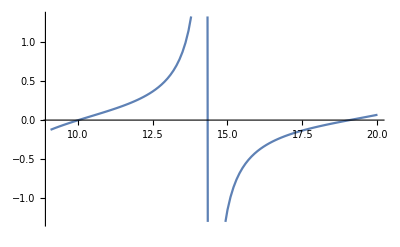

InterpolatingFunction[{{9.1, 20.}}, <>]

```mathematica
StepE=Table[g, {g, sp, Eg,dx}];
dots=Transpose[{StepE,-Im[c2^-1]}];
ListLinePlot[dots]
iFun=Interpolation[dots]
```

```mathematica
dots1=Transpose[{StepE,-Im[c2^-1]}];
ListLinePlot[dots1]
iFun1=Interpolation[dots1]
```

-Graphics-

InterpolatingFunction[{{9.1, 20.}}, <>]

```mathematica
s$rule=N[FindRoot[iFun1[x],{x,17.9}],15];
x$sol=N[x/.s$rule,10]
```

19.0719